# Quantum Physics

## The Harmonic Oscillator (2.3)

William Arnold

Let’s set up the stationary states

```mathematica
$Assumptions = {x, t, m, ω, ℏ} ∈ Reals && t ≥ 0 && n ∈ Integers && n ≥ 0 && ω > 0 && m > 0 && ℏ > 0;
p0 = (m ω / (π ℏ))^(1/4) Exp[- m ω x^2 / (2 ℏ)];
pop[f_] := - ⅈ ℏ D[f, x];
aplus[f_] := 1/Sqrt[2 ℏ m ω] (- ⅈ pop[f] + m ω x f);
ψ[n_] := Sqrt[1/Factorial[n]] Nest[aplus, p0, n] // Simplify;
ϕ[n_] :=  Exp[- ⅈ (n + (1/2)) t / ℏ]
FixConstants[f_] := Replace[Simplify[f],{ℏ -> 1, m -> 1, ω -> 1, π -> 1}, 50000];
Subscript[Ψ, n][x_, t_, n_] := ψ[n]ϕ[n] // Simplify // FixConstants
```

Now we can plot some functions, we’ll start with this one:

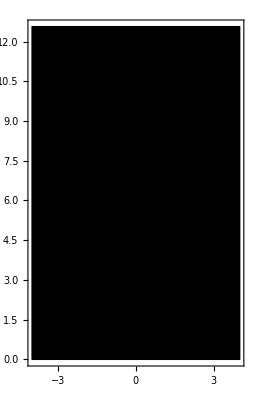

```mathematica
γ[x_, t_] = 1/(√3)(Subscript[Ψ, n][x, t, 2] + Subscript[Ψ, n][x, t, 3] + Subscript[Ψ, n][x, t, 4]) // Simplify;
ComplexPlot[γ[Re[z], Im[z]], {z, -4, 4 + 4 π ⅈ}, PlotLegends -> Automatic]
```

```mathematica
frame[t_] := ReImPlot[γ[x,t], {x, -4, 4}, PlotRange -> {-1.5, 1.5}, PlotLegends -> Automatic];
Animate[frame[t], {t, 0, 4 π}, RefreshRate -> 30, AnimationRate -> 0.15]
```

### Problems

#### Problem 2.10

a) Construct ψ_2

```mathematica
ψ[2] // FullSimplify
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) (2 m x^2 ω-ℏ) ((m ω)/ℏ)^(1/4))/(√2 π^(1/4) ℏ)

b) Sketch ψ_0, ψ_1, ψ_2

{ⅇ^(-x^2/2),√2 ⅇ^(-x^2/2) x,(ⅇ^(-x^2/2) (-1+2 x^2))/(√2)}

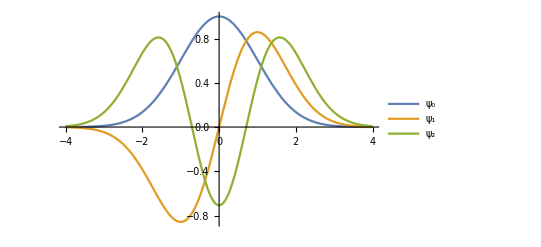

```mathematica
{ps0[x_], ps1[x_], ps2[x_]} = FixConstants /@ {p0, ψ[1], ψ[2]} 
Plot[{ps0[x], ps1[x], ps2[x]}, {x, -4, 4}, PlotLegends -> {Subscript[ψ, 0], Subscript[ψ, 1], Subscript[ψ, 2]}]
```

c) Check the orthogonality of ψ_0, ψ_1, and ψ_2 by explicit integration

```mathematica
{Integrate[p0 ψ[1], {x, -∞, ∞}], 
 Integrate[p0 ψ[2], {x, -∞, ∞}], 
 Integrate[ψ[1] ψ[2], {x, -∞, ∞}]}
```

{0,0,0}

#### Problem 2.11

a) Compute ⟨x⟩, ⟨p⟩, ⟨x^2⟩, ⟨p^2⟩ for the states ψ_0 and ψ_1
First we compute for ψ_0

```mathematica
Subscript[Εx, 0] = Integrate[ψ[0] x ψ[0], {x, -∞, ∞}]
Subscript[Εp, 0] = Integrate[ψ[0] pop[ψ[0]], {x, -∞, ∞}]
Subscript[Εx^2, 0] = Integrate[ψ[0] x^2 ψ[0], {x, -∞, ∞}]
Subscript[Εp^2, 0] = Integrate[ψ[0] pop[pop[ψ[0]]], {x, -∞, ∞}]
```

0

0

ℏ/(2 m ω)

(m ω ℏ)/2

Now we compute for ψ_1

```mathematica
Subscript[Εx, 1] = Integrate[ψ[1] x ψ[1], {x, -∞, ∞}]
Subscript[Εp, 1] = Integrate[ψ[1] pop[ψ[1]], {x, -∞, ∞}]
Subscript[Εx^2, 1] = Integrate[ψ[1] x^2 ψ[1], {x, -∞, ∞}]
Subscript[Εp^2, 1] = Integrate[ψ[1] pop[pop[ψ[1]]], {x, -∞, ∞}]
```

0

0

(3 ℏ)/(2 m ω)

(3 m ω ℏ)/2

b) Check the uncertainty principle for these states

```mathematica
Subscript[Var, x,0] = Subscript[Εx^2, 0] - (Subscript[Εx, 0])^2;
Subscript[Var, p,0] = Subscript[Εp^2, 0] - (Subscript[Εp, 0])^2;
Sqrt[Subscript[Var, x,0] Subscript[Var, p,0]] // Simplify

Subscript[Var, x,1]= Subscript[Εx^2, 1] - (Subscript[Εx, 1])^2;
Subscript[Var, p,1] = Subscript[Εp^2, 1] - (Subscript[Εp, 1])^2;
Sqrt[Subscript[Var, x,1] Subscript[Var, p,1]] // Simplify
```

ℏ/2

(3 ℏ)/2

So we see that ψ_0 has the minimum uncertainty

c) Compute ⟨T⟩ and ⟨V⟩ for these states (Note: T is kinetic energy, V is potential energy)
Note that we have ⟨T⟩ = 1/(2m)⟨p^2⟩, ⟨V⟩ = 1/2k ⟨x^2⟩ = 1/2 ω^2 m⟨x^2⟩

```mathematica
Subscript[⟨T⟩, 0] = Subscript[Εp^2, 0] / (2m)
Subscript[⟨T⟩, 1] = Subscript[Εp^2, 1] / (2m)
Subscript[⟨V⟩, 0] = 1/2 ω^2 m Subscript[Εx^2, 0]
Subscript[⟨V⟩, 1] = 1/2 ω^2 m Subscript[Εx^2, 1]
```

(ω ℏ)/4

(3 ω ℏ)/4

(ω ℏ)/4

(3 ω ℏ)/4

And we see their sums are

```mathematica
Subscript[⟨T⟩, 0] + Subscript[⟨V⟩, 0] // Simplify
Subscript[⟨T⟩, 1] + Subscript[⟨V⟩, 1] // Simplify
```

(ω ℏ)/2

(3 ω ℏ)/2

Which are E_0 and E_1 respectively! So the sums of the expected potential and kinetic energies are exactly the total energy of the system. By linearity of expectation we actually get that ⟨T + V ⟩ = E_n here.